```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
```

```mathematica
Clear[d2]
d2[n_,x_,k_]:=d2[n,x,k]=-d2[n,x,k-1]-x Sum[ d2[n/(j x),x,k-1],{j,1,n}]
d2[n_,x_,0]:=UnitStep[n-1]
ld2[n_,x_] := Sum[ (-1)^(k+1)/k d2[n,x,k],{k,1,3Log2@n}]
```

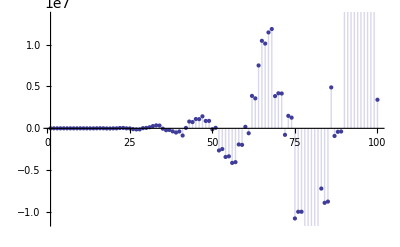

```mathematica
DiscretePlot[ld2[n,1.2],{n,1,100}]
```

```mathematica
Table[d2[100,1.3,k],{k,0,16}]
```

{1,-99.8,619.41,-2620.98,9079.25,-27745.2,77846.1,-204231.,507862.,-1.21081×10^6,2.7898×10^6,-6.23944×10^6,1.35731×10^7,-2.87525×10^7,5.93833×10^7,-1.19772×10^8,2.36387×10^8}

```mathematica
Sum[ ((-1)^(k+1)/k (j/y)^k)/Log[n],{k,1,Infinity}]
```

Log[(j+y)/y]/Log[n]

```mathematica
Sum[ ((-1)^(k+1)/k ((j)/y)^k)/Log[n],{k,1,Infinity}]+Sum[ ((-1)^(k+1)/k ((t)/y)^k)/Log[n],{k,1,Infinity}]
```

Log[(j+y)/y]/Log[n]+Log[(t+y)/y]/Log[n]

```mathematica
Sum[ ((-1)^(k+1)/k (j/y)^k),{k,1,Infinity}]
```

Log[(j+y)/y]

```mathematica
Sum[ ((-1)^(k+1)/k (n-1)^-k),{k,1,Infinity}]
```

Log[n/(-1+n)]

```mathematica
Sum[ ((-1)^(k+1)/k ((j)/y)^k)/Log[n]+((-1)^(k+1)/k ((t)/y)^k)/Log[n],{k,1,Infinity}]
```

(Log[(j+y)/y]+Log[(t+y)/y])/Log[n]

```mathematica
Sum[ ((-1)^(k+1)/k ((j)/y)^k)+((-1)^(k+1)/k ((t)/y)^k),{k,1,Infinity}]
```

Log[(j+y)/y]+Log[(t+y)/y]

```mathematica
Sum[ ((-1)^(k+1)/k (j/y)^k)+((-1)^(k+1)/k (t/y)^k),{k,1,Infinity}]
```

Log[(j+y)/y]+Log[(t+y)/y]

```mathematica
Sum[ ((-1)^(k+1)/k( (j/y)^k)+( (t/y)^k)),{k,1,Infinity}]
```

(-t+t Log[(j+y)/y]-y Log[(j+y)/y])/(t-y)

```mathematica
Sum[ ((-1)^(k+1)/k( (j/y)^k+ (t/y)^k)),{k,1,Infinity}]
```

Log[(j+y)/y]+Log[(t+y)/y]

```mathematica
Sum[ ((-1)^(k+1)/k( (j^k/y^k)+ (t^k/y^k))),{k,1,Infinity}]
```

Log[(j+y)/y]+Log[(t+y)/y]

```mathematica
Sum[ (-1)^(k+1)/k( j^k/y^k+ t^k/y^k),{k,1,Infinity}]
```

Log[(j+y)/y]+Log[(t+y)/y]

```mathematica
Sum[ (-1)^(k+1)/k( (j^k+t^k)/y^k),{k,1,Infinity}]
```

Log[(j+y)/y]+Log[(t+y)/y]

```mathematica
Sum[ (-1)^(k+1)/k( n-1)^k,{k,1,Infinity}]
```

Log[n]

```mathematica
Grid@Table[ (-1)^(k-j) (-1)^(j-m) Bin[z,k] Binomial[k,j] Binomial[j,m] f[ n y^(j-k), m],{j,0,k},{m,0,j}]/.k->0
```

Table::iterb: Iterator {j, 0, k} does not have appropriate bounds.

Bin[z,0] f[n,0]

```mathematica
Grid@Table[ (-1)^(k-j) (-1)^(j-m) Bin[z,k] Binomial[k,j] Binomial[j,m] f[ n y^(j-k), m],{j,0,k},{m,0,j}]/.k->1
```

Table::iterb: Iterator {j, 0, k} does not have appropriate bounds.

-Bin[z,1] f[n/y,0] | 
-Bin[z,1] f[n,0] | Bin[z,1] f[n,1]

```mathematica
Grid@Table[ (-1)^(k-j) (-1)^(j-m) Bin[z,k] Binomial[k,j] Binomial[j,m] f[ n y^(j-k), m],{j,0,k},{m,0,j}]/.k->2
```

Table::iterb: Iterator {j, 0, k} does not have appropriate bounds.

Bin[z,2] f[n/y^2,0] |  | 
2 Bin[z,2] f[n/y,0] | -2 Bin[z,2] f[n/y,1] | 
Bin[z,2] f[n,0] | -2 Bin[z,2] f[n,1] | Bin[z,2] f[n,2]

```mathematica
Grid@Table[ (-1)^(k-j) (-1)^(j-m) Bin[z,k] Binomial[k,j] Binomial[j,m] f[ n y^(j-k), m],{j,0,k},{m,0,j}]/.k->3
```

Table::iterb: Iterator {j, 0, k} does not have appropriate bounds.

-Bin[z,3] f[n/y^3,0] |  |  | 
-3 Bin[z,3] f[n/y^2,0] | 3 Bin[z,3] f[n/y^2,1] |  | 
-3 Bin[z,3] f[n/y,0] | 6 Bin[z,3] f[n/y,1] | -3 Bin[z,3] f[n/y,2] | 
-Bin[z,3] f[n,0] | 3 Bin[z,3] f[n,1] | -3 Bin[z,3] f[n,2] | Bin[z,3] f[n,3]

```mathematica
Grid@Table[ (-1)^(k-j) (-1)^(j-m) Bin[z,k] Binomial[k,j] Binomial[j,m] f[ n y^(j-k), m],{j,0,k},{m,0,j}]/.k->4
```

Table::iterb: Iterator {j, 0, k} does not have appropriate bounds.

Bin[z,4] f[n/y^4,0] |  |  |  | 
4 Bin[z,4] f[n/y^3,0] | -4 Bin[z,4] f[n/y^3,1] |  |  | 
6 Bin[z,4] f[n/y^2,0] | -12 Bin[z,4] f[n/y^2,1] | 6 Bin[z,4] f[n/y^2,2] |  | 
4 Bin[z,4] f[n/y,0] | -12 Bin[z,4] f[n/y,1] | 12 Bin[z,4] f[n/y,2] | -4 Bin[z,4] f[n/y,3] | 
Bin[z,4] f[n,0] | -4 Bin[z,4] f[n,1] | 6 Bin[z,4] f[n,2] | -4 Bin[z,4] f[n,3] | Bin[z,4] f[n,4]

```mathematica
Sum[ (-1)^k Binomial[z,k] ,{k,0,Infinity}]f[n,0]
```

f[n,0] HypergeometricPFQ[{-z},{},1]

```mathematica
Sum[ (-1)^k Binomial[k,k-1] Binomial[z,k] ,{k,0,Infinity}]f[n/y,0]
```

-z f[n/y,0] HypergeometricPFQ[{1-z},{},1]

```mathematica
Sum[ (-1)^k Binomial[k,k-2]Binomial[z,k],{k,0,Infinity}] f[n/y^2,0]
```

1/2 f[n/y^2,0] (z HypergeometricPFQ[{1-z},{},1]-z HypergeometricPFQ[{2,1-z},{1},1])

```mathematica
Table[Binomial[k,k-1],{k,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Clear[dd]
dd[n_, y_, k_] := dd[n,y,k]=Sum[ dd[Floor[n/j],y,k-1],{j,y,n}]
dd[n_, y_, 0] := UnitStep[n-1]
dz[n_,y_,z_]:=Sum[ bin[z,k] dd[n,y,k],{k,0,Log[y,n]}]
da[n_,y_,k_]:=Sum[bin[k,j]dd[n (y^(j-k)),y+1,j],{j,0,k}]
db[n_,y_,j_]:=Sum[(-1)^(j-m)bin[j,m]dz[n,y,m],{m,0,j}]
dzp1[n_,y_,z_]:=Sum[ bin[z,k] Sum[bin[k,j]dd[n(y^(j-k)),y+1,j],{j,0,k}],{k,0,Log[y,n]}]
dzm1[n_,y_,z_]:=Sum[ bin[z,k] Sum[(-1)^(k-j)bin[k,j]dd[n((y-1)^(j-k)),y-1,j],{j,0,k}],{k,0,Log[y,n]}]
dzp1a[n_,y_,z_]:=Sum[ bin[z,k] Sum[bin[k,j]Sum[(-1)^(j-m)bin[j,m]dz[n(y^(j-k)),y+1,m],{m,0,j}],{j,0,k}],{k,0,Log[y,n]}]
dzm1a[n_,y_,z_]:=Sum[ bin[z,k] Sum[(-1)^(k-j)bin[k,j]Sum[(-1)^(j-m)bin[j,m]dz[n((y-1)^(j-k)),y-1,m],{m,0,j}],{j,0,k}],{k,0,Log[y,n]}]
dzp1b[n_,y_,z_]:=Sum[bin[z,k]bin[k,j](-1)^(j-m)bin[j,m]dz[n(y^(j-k)),y+1,m],{k,0,Log[y,n]},{j,0,k},{m,0,j}]
dzm1b[n_,y_,z_]:=Sum[  bin[z,k]bin[k,j]bin[j,m](-1)^(k-m)dz[n((y-1)^(j-k)),y-1,m],{k,0,Log[y,n]},{j,0,k},{m,0,j}]
```

```mathematica
Expand@dz[100,2,z]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
Expand@dz[100,3,z]
```

1+(341 z)/12+(1391 z^2)/24+(139 z^3)/12+z^4/24

```mathematica
Expand@dzp1[100,2,z]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
dd[100,2,2]
```

283

```mathematica
da[100,2,2]
```

283

```mathematica
Expand@dzp1b[100,3,z]
```

1+(341 z)/12+(1391 z^2)/24+(139 z^3)/12+z^4/24

```mathematica
Expand@dz[100,3,z]
```

1+(341 z)/12+(1391 z^2)/24+(139 z^3)/12+z^4/24

```mathematica
db[100,2,2]
```

283

```mathematica
Binomial[k,k-2]
```

1/2 (-1+k) k

```mathematica
Sum[ Binomial[z,k]x^(k),{k,0,Infinity}]
```

(1+x)^z

```mathematica
Sum[ Binomial[z,k]k x^(k-1),{k,0,Infinity}]
```

(1+x)^(-1+z) z

```mathematica
Sum[ Binomial[z,k](k)(k-1)/2  x^(k-2),{k,0,Infinity}]
```

1/2 (1+x)^(-2+z) (-1+z) z

```mathematica
Sum[ Binomial[z,k](k)(k-1)(k-2)/6  x^(k-3),{k,0,Infinity}]
```

1/6 (1+x)^(-3+z) z (2-3 z+z^2)

```mathematica
Sum[ Binomial[z,k] x^(k),{k,0,Infinity}]
```

(1+x)^z

```mathematica
Sum[ Binomial[z,k](1+Zeta[s,a])^(z-k),{k,0,Infinity}]
```

(1+Zeta[s,a])^z ((2+Zeta[s,a])/(1+Zeta[s,a]))^z

```mathematica
N@(2+Zeta[2,5])^2
```

4.93428

```mathematica
Binomial[k,k-1]
```

k

```mathematica
Binomial[k,k-2]
```

1/2 (-1+k) k

```mathematica
Sum[ Binomial[z,k]Binomial[k,k-2]  x^(k-2),{k,0,Infinity}]
```

1/2 (1+x)^(-2+z) (-1+z) z

```mathematica
Sum[ Binomial[z,k]Binomial[k,k-3]  x^(k-3),{k,0,Infinity}]
```

1/6 (1+x)^(-3+z) z (2-3 z+z^2)

```mathematica
Binomial[z,1]
```

z

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Clear[dd]
dd[n_, y_, k_] := dd[n,y,k]=Sum[ dd[Floor[n/j],y,k-1],{j,y,n}]
dd[n_, y_, 0] := UnitStep[n-1]
dz[n_,y_,z_]:=Sum[ bin[z,k] dd[n,y,k],{k,0,Log[y,n]}]
da[n_,y_,k_]:=Sum[bin[k,j]dd[n (y^(j-k)),y+1,j],{j,0,k}]
dza[n_,y_,z_]:=Sum[ bin[z,k] Sum[bin[k,j]dd[n (y^(j-k)),y+1,j],{j,0,k}],{k,0,Log[y,n]}]
dzb[n_,y_,z_]:=Sum[ bin[z,k] (dd[n ,y+1,k]+Sum[bin[k,j]dd[n (y^(j-k)),y+1,j],{j,0,k-1}]),{k,0,Log[y,n]}]
dzc[n_,y_,z_]:=Sum[ bin[z,k] dd[n ,y+1,k],{k,0,Log[y,n]}]+Sum[ bin[z,k] Sum[bin[k,j]dd[n (y^(j-k)),y+1,j],{j,0,k-1}],{k,0,Log[y,n]}]
dzd[n_,y_,z_]:= dz[n ,y+1,z]+Sum[ bin[z,k] Sum[bin[k,j]dd[n (y^(j-k)),y+1,j],{j,0,k-1}],{k,0,Log[y,n]}]
dze[n_,y_,z_]:= dz[n ,y+1,z]+Sum[ bin[z,k] bin[k,k-1]dd[n (y^(-1)),y+1,k-1],{k,0,Log[y,n]}]+Sum[ bin[z,k] Sum[bin[k,j]dd[n (y^(j-k)),y+1,j],{j,0,k-2}],{k,0,Log[y,n]}]
dzf[n_,y_,z_]:= dz[n ,y+1,z]+z dz[n/y ,y+1,z-1]+Sum[ bin[z,k] Sum[bin[k,j]dd[n (y^(j-k)),y+1,j],{j,0,k-2}],{k,0,Log[y,n]}]
dzg[n_,y_,z_]:= dz[n ,y+1,z]+Binomial[z,1] dz[n/y ,y+1,z-1]+Binomial[z,2] dz[n/y^2 ,y+1,z-2]+Sum[ bin[z,k] Sum[bin[k,j]dd[n (y^(j-k)),y+1,j],{j,0,k-3}],{k,0,Log[y,n]}]
dzh[n_,y_,z_]:= Sum[ bin[z,k] dz[n/y^k ,y+1,z-k],{k,0,Log[y,n]}]
dzi[n_,y_,z_]:= If[ n<y,1,Sum[ bin[z,k] dzi[n/y^k ,y+1,z-k],{k,0,Log[y,n]}]]
dzj[n_,y_,z_]:= Sum[(-1)^k bin[z,k] dz[n/(y-1)^k ,y-1,z-k],{k,0,Log[y-1,n]}]
d2z[n_,y_,z_,t_] := Sum[ (-1)^k bin[z,k] dz[n ,y,z-k],{k,0,t}]


dd[100,3,3]
```

71

```mathematica
Expand@dz[100,3,3]
```

924

```mathematica
dza[100,3,3]
```

924

```mathematica
dzb[100,3,3]
```

924

```mathematica
dzc[100,3,3]
```

924

```mathematica
dzd[100,3,3]
```

924

```mathematica
dzf[100,3,3]
```

924

```mathematica
Expand@dzg[100,3,3]
```

924

```mathematica
Expand@dzh[100,3,z]
```

1+(341 z)/12+(1391 z^2)/24+(139 z^3)/12+z^4/24

```mathematica
Expand@dzj[100,3,z]
```

1+(341 z)/12+(1391 z^2)/24+(139 z^3)/12+z^4/24

```mathematica
Expand@dz[1000,5,z]
```

1-(49 z)/4+(18821 z^2)/24+(893 z^3)/4+(19 z^4)/24

```mathematica
Expand@dzh[1000,32,z]
```

1+969 z

```mathematica
N[1000^(1/2)]
```

31.6228

```mathematica
Expand[dzi[100,2,z]]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
1000-32+1
```

969

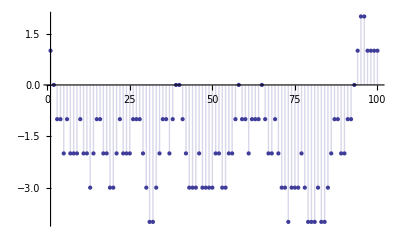

```mathematica
DiscretePlot[dzi[n,2,-1],{n,1,100}]
```

```mathematica
Grid@Table[Binomial[-k,j],{k,0,6},{j,0,6}]
```

1 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -2 | 3 | -4 | 5 | -6 | 7
1 | -3 | 6 | -10 | 15 | -21 | 28
1 | -4 | 10 | -20 | 35 | -56 | 84
1 | -5 | 15 | -35 | 70 | -126 | 210
1 | -6 | 21 | -56 | 126 | -252 | 462